```mathematica
Φ[t_,x_,y_,z_]:=1/Sqrt[x[t]^2+y[t]^2]
```

```mathematica
q=1;
m=1;
tf=2500;
```

```mathematica
usol=Solve[1/(Sqrt[1-u^2]^4)u^2/r==1/r^2,u];
uinit=u/.usol[[2,1]]
```

(√(2+r-√r √(4+r)))/(√2)

```mathematica
u[r_]:=(√(2+r-√r √(4+r)))/(√2)
```

```mathematica
γ[t_]:=1/Sqrt[1-(ux[t]^2+uy[t]^2)];
```

```mathematica
eqx=D[ux[t],t]==q/(γ[t]^4 m)((1+γ[t]^2 ux[t]^2)D[Φ[t,x,y,z],x[t]]
+γ[t]^2 ux[t](D[Φ[t,x,y,z],t]+
uy[t]D[Φ[t,x,y,z],y[t]]));
eqy=D[uy[t],t]==q/(γ[t]^4 m)((1+γ[t]^2 uy[t]^2)D[Φ[t,x,y,z],y[t]]
+γ[t]^2 uy[t](D[Φ[t,x,y,z],t]+
ux[t]D[Φ[t,x,y,z],x[t]]));
```

```mathematica
sol1=NDSolve[{
eqx,eqy,
D[x[t],t]==ux[t],
D[y[t],t]==uy[t],
ux[0]==0,uy[0]==u[x[0]],
x[0]==3,y[0]==0},
{ux[t],uy[t],x[t],y[t]},{t,0,tf}];
```

```mathematica
u[3]//N
```

0.45685

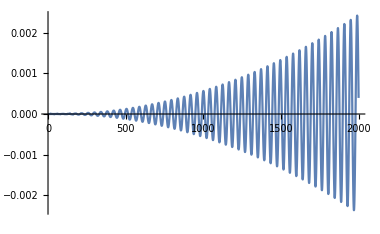

```mathematica
Plot[{x[t]-3Cos[ (u[3] t)/3]/.sol1},{t,0,2000}]
```

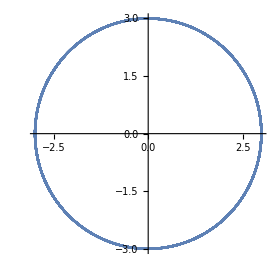

```mathematica
ParametricPlot[{x[t],y[t]}/.sol1,{t,0,tf/2}]
```